```mathematica
a = 1;
```

```mathematica
G[phi_,theta_]:=Exp[-Cos[phi+2*theta]]*(Pi - theta)*theta
```

```mathematica
Int = NIntegrate[((a-r^2)*G[phi,theta])^2*r^2*Sin[theta],{r,0,a},{theta,0,Pi},{phi, 0 ,2*Pi}];
```

```mathematica
B=1/Sqrt[Int]
```

```mathematica
0.32792284570150765
```

```mathematica
n =1 ; l=0; m =0;
```

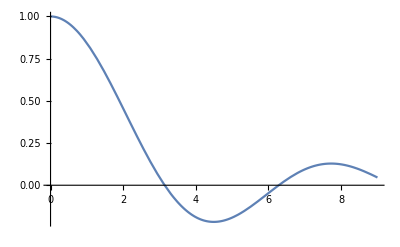

```mathematica
Plot[SphericalBesselJ[l,r],{r,0,9}]
```

```mathematica
FindRoot[SphericalBesselJ[l,r],{r,3}]
```

{r→3.14159}

```mathematica
Beta6= Pi;
```

```mathematica
NIntegrate[Conjugate[SphericalBesselJ[l,Pi*r]*Sqrt[2/a^3]/SphericalBesselJ[l+1,Beta6]*SphericalHarmonicY[l,m,theta,phi]]*(a-r^2)*G[phi,theta]*r^2*Sin[theta],{r,0,a},{theta,0,Pi},{phi, 0 ,2*Pi}]
```

2.45645

```mathematica
SphBesselRoot[l_,k_]:=N[BesselJZero[l+1/2,k]];
```

```mathematica
SphBesselRoot[5,4]
```

19.6532